# QCD calculation: Webber et al. Sec. 7

-Graphics-

## Two-jet cross sections (Only QCD; mass ignored) : Ellis-Stirling-Webber Sec.7.5

-Graphics-

### Initialization

```mathematica
Exit[];
```

```mathematica
$Language="English";
<<FeynArts`
<<FormCalc`
```

FeynArts 3.8

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

last revised 1 Jul 13

FormCalc 8.2

by Thomas Hahn

last revised 2 Jul 13

### Create Topology (and also ignore helicities)

```mathematica
topologies=CreateTopologies[0,2->2];
_Hel=0;
```

### q q' -> q q'

loading generic model file /Users/misho/Documents/Mathematica/lib/FeynArts-3.8/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/misho/Documents/Mathematica/lib/FeynArts-3.8/Models/SMQCD.mod

loading classes model file /Users/misho/Documents/Mathematica/lib/FeynArts-3.8/Models/SM.mod

> 46 particles (incl. antiparticles) in 18 classes

> $CounterTerms are ON

> 93 vertices

> 120 counter terms of order 1

> 6 counter terms of order 2

classes model {SMQCD} initialized

Excluding 0 Generic, 6 Classes, and 6 Particles fields

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 0 Classes insertions

> Top. 3: 1 Classes insertion

> Top. 4: 0 Classes insertions

Restoring 0 Generic, 6 Classes, and 6 Particles fields

in total: 1 Classes insertion

> Top. 1: 1 diagram

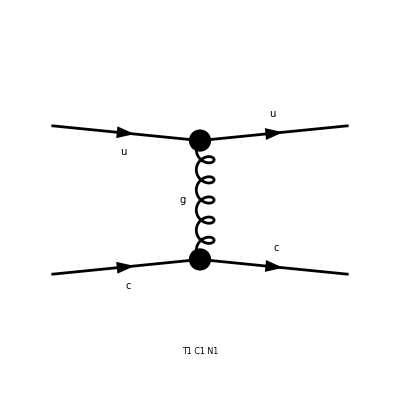

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

preparing FORM code in /Users/misho/fc-amp-1.frm

running FORM...

ok

```mathematica
diag=InsertFields[topologies,{F[3,{1}],F[3,{2}]}->{F[3,{1}],F[3,{2}]},InsertionLevel->{Classes},
Model->"SMQCD",
ExcludeParticles->{V[1],V[2],V[3],V[4],S[1],S[2]}];
Paint[diag];
ClearProcess[];
amp=CalcFeynAmp[CreateFeynAmp[diag],FermionChains->VA];
```

```mathematica
SquaredME[amp]//.HelicityME[amp]//FullSimplify
```

> 16 helicity matrix elements

preparing FORM code in /Users/misho/fc-hel-1.frm

running FORM...

ok

1/9 Alfas2 π^2 (4 MC2^2+4 MU2^2+T^2+(S-U)^2+2 MC2 (4 MU2-S+T-U)-2 MU2 (S-T+U)) Den[T,0]^2 (9 Mat[SUN1,SUN1]-3 (Mat[SUN1,SUN2]+Mat[SUN2,SUN1])+Mat[SUN2,SUN2])

```mathematica
%//.Abbr[]
```

1/9 Alfas2 π^2 (4 MC2^2+4 MU2^2+T^2+(S-U)^2+2 MC2 (4 MU2-S+T-U)-2 MU2 (S-T+U)) Den[T,0]^2 (9 Mat[SUNT[Col1,Col4] SUNT[Col2,Col3],SUNT[Col1,Col4] SUNT[Col2,Col3]]-3 (Mat[SUNT[Col1,Col4] SUNT[Col2,Col3],SUNT[Col1,Col3] SUNT[Col2,Col4]]+Mat[SUNT[Col1,Col3] SUNT[Col2,Col4],SUNT[Col1,Col4] SUNT[Col2,Col3]])+Mat[SUNT[Col1,Col3] SUNT[Col2,Col4],SUNT[Col1,Col3] SUNT[Col2,Col4]])

```mathematica
SquaredME[amp]//.HelicityME[amp]//.ColourME[amp]//FullSimplify
```

> 16 helicity matrix elements

preparing FORM code in /Users/misho/fc-hel-1.frm

running FORM...

ok

8 Alfas2 π^2 (4 MC2^2+4 MU2^2+T^2+(S-U)^2+2 MC2 (4 MU2-S+T-U)-2 MU2 (S-T+U)) Den[T,0]^2

```mathematica
%//.Subexpr[]//.{Alfas2->(gs^2/(4π))^2,MC2->0,MU2->0,Den[a_,b_]:>1/(a-b)}
```

(gs^4 (T^2+(S-U)^2))/(2 T^2)

```mathematica
FullSimplify[gs^4 4/9(S^2+U^2)/T^2//.U->-S-T]
```

(4 gs^4 (2 S^2+2 S T+T^2))/(9 T^2)

ggggg..................
HelicityME takes AVARAGE, and ColourME takes SUM!!!!!!!!!!!!!!

#### LESSON

×2 for each FINAL fermion

DIVIDE by INITIAL colour factor

```mathematica
FullSimplify[(SquaredME[amp]//.HelicityME[amp]//.ColourME[amp])*2^2/3^2//.{Alfas2->(gs^2/(4π))^2,MC->0,MU->0,MC2->0,MU2->0,Den[a_,b_]:>1/(a-b)}]
FullSimplify[gs^4 4/9(S^2+U^2)/T^2//.U->-S-T]
```

> 16 helicity matrix elements

preparing FORM code in /Users/misho/fc-hel-1.frm

running FORM...

ok

(2 gs^4 (T^2+(S-U)^2))/(9 T^2)

(4 gs^4 (2 S^2+2 S T+T^2))/(9 T^2)

### q q' -> q q' (Again)

```mathematica
diag=InsertFields[topologies,{F[3,{1}],F[3,{2}]}->{F[3,{1}],F[3,{2}]},InsertionLevel->{Classes},
Model->"SMQCD",
ExcludeParticles->{V[1],V[2],V[3],V[4],S[1],S[2]}];
Paint[diag];
ClearProcess[];
amp=CalcFeynAmp[CreateFeynAmp[diag],FermionChains->VA];
FullSimplify[(SquaredME[amp]//.HelicityME[amp]//.ColourME[amp])*2^2/3^2//.Subexpr[]//.{Alfas2->(gs^2/(4π))^2,MC->0,MU->0,MC2->0,MU2->0,Den[a_,b_]:>1/(a-b)}//.U->-S-T]
FullSimplify[gs^4 4/9(S^2+U^2)/T^2//.U->-S-T]
```

Excluding 0 Generic, 6 Classes, and 6 Particles fields

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 0 Classes insertions

> Top. 3: 1 Classes insertion

> Top. 4: 0 Classes insertions

Restoring 0 Generic, 6 Classes, and 6 Particles fields

in total: 1 Classes insertion

> Top. 1: 1 diagram

-Graphics-

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

preparing FORM code in /Users/misho/fc-amp-1.frm

running FORM... running FORM...

ok

> 16 helicity matrix elements

preparing FORM code in /Users/misho/fc-hel-1.frm

ok

(4 gs^4 (2 S^2+2 S T+T^2))/(9 T^2)

(4 gs^4 (2 S^2+2 S T+T^2))/(9 T^2)

### g q -> g q

Excluding 0 Generic, 6 Classes, and 6 Particles fields

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 1 Classes insertion

> Top. 3: 1 Classes insertion

> Top. 4: 1 Classes insertion

Restoring 0 Generic, 6 Classes, and 6 Particles fields

in total: 3 Classes insertions

> Top. 1: 1 diagram

> Top. 2: 1 diagram

> Top. 3: 1 diagram

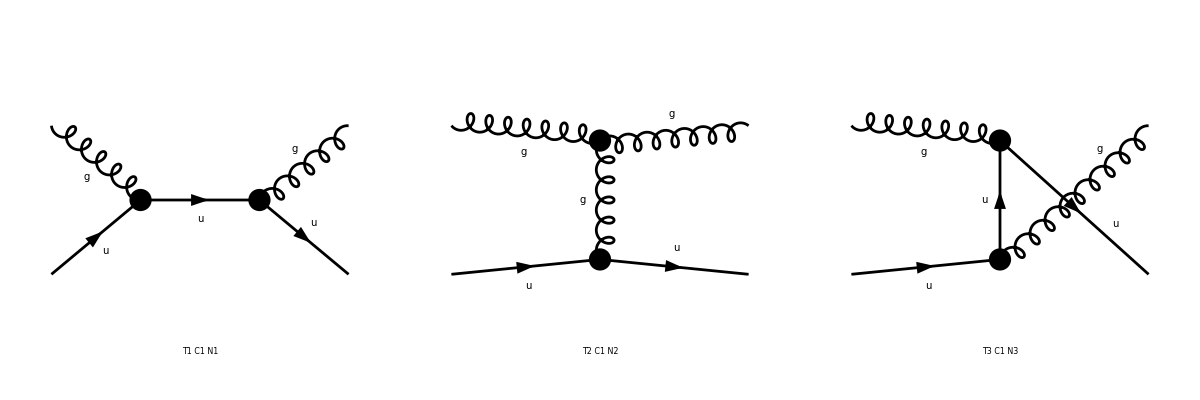

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

> Top. 2: 1 Classes amplitude

> Top. 3: 1 Classes amplitude

in total: 3 Classes amplitudes

preparing FORM code in /Users/misho/fc-amp-1.frm

running FORM... running FORM...

ok

> 16 helicity matrix elements

preparing FORM code in /Users/misho/fc-hel-1.frm

ok

1/12 (128/3 Alfas2 (Abb14+2 MU2 Pair2 Pair7) π^2 Den[S,MU2]^2+32/3 Abb21 Alfas2 Pair2 π^2 Den[S,MU2] (4 Den[S,MU2]+8 Den[T,0])+32/3 Abb11 Alfas2 Pair1 Pair7 π^2 Den[S,MU2] (4 Den[S,MU2]+8 Den[T,0])+32/3 Abb1 Alfas2 Pair2 π^2 Pair1^* Den[S,MU2] (4 Den[S,MU2]+8 Den[T,0])-32/3 Abb12 Alfas2 π^2 Pair2^* Den[S,MU2] (4 Den[S,MU2]+8 Den[T,0])+8/3 Abb5 Alfas2 Pair2 π^2 Pair1^* (4 Den[S,MU2]+8 Den[T,0])^2-8/3 Alfas2 Pair1 π^2 (MU2-S) (MU2-U) Pair1^* (4 Den[S,MU2]+8 Den[T,0])^2+8/3 Abb6 Alfas2 Pair1 π^2 Pair2^* (4 Den[S,MU2]+8 Den[T,0])^2+8/3 Alfas2 (Abb19-2 MU2) Pair2 π^2 Pair2^* (4 Den[S,MU2]+8 Den[T,0])^2+256/3 Abb18 Alfas2 π^2 Den[S,MU2] (Pair3 Den[S,MU2]+Pair4 Den[T,0])-64/3 Alfas2 (-Abb17+2 MU2 Pair2) π^2 Pair1^* (4 Den[S,MU2]+8 Den[T,0]) (Pair3 Den[S,MU2]+Pair4 Den[T,0])+64/3 Alfas2 (Abb15+2 MU2 Pair14) π^2 Pair2^* (4 Den[S,MU2]+8 Den[T,0]) (Pair3 Den[S,MU2]+Pair4 Den[T,0])+256/3 Abb13 Alfas2 π^2 Den[S,MU2] (Pair3^* Den[S,MU2]+Pair4^* Den[T,0])+64/3 Alfas2 (Abb20+2 MU2 Pair15) Pair2 π^2 (4 Den[S,MU2]+8 Den[T,0]) (Pair3^* Den[S,MU2]+Pair4^* Den[T,0])-64/3 Alfas2 Pair1 (-Abb22+2 MU2 Pair7) π^2 (4 Den[S,MU2]+8 Den[T,0]) (Pair3^* Den[S,MU2]+Pair4^* Den[T,0])+512/3 Alfas2 (Abb16-2 MU2) π^2 (Pair3 Den[S,MU2]+Pair4 Den[T,0]) (Pair3^* Den[S,MU2]+Pair4^* Den[T,0])-32/3 Alfas2 (Abb14+2 MU2 Pair2 Pair7) π^2 Den[S,MU2] Den[U,MU2]-4/3 Abb21 Alfas2 Pair2 π^2 (4 Den[S,MU2]+8 Den[T,0]) Den[U,MU2]-4/3 Abb11 Alfas2 Pair1 Pair7 π^2 (4 Den[S,MU2]+8 Den[T,0]) Den[U,MU2]-4/3 Abb1 Alfas2 Pair2 π^2 Pair1^* (4 Den[S,MU2]+8 Den[T,0]) Den[U,MU2]+4/3 Abb12 Alfas2 π^2 Pair2^* (4 Den[S,MU2]+8 Den[T,0]) Den[U,MU2]-32/3 Abb18 Alfas2 π^2 (Pair3 Den[S,MU2]+Pair4 Den[T,0]) Den[U,MU2]-32/3 Abb13 Alfas2 π^2 (Pair3^* Den[S,MU2]+Pair4^* Den[T,0]) Den[U,MU2]+128/3 Alfas2 (Abb14+2 MU2 Pair2 Pair7) π^2 Den[U,MU2]^2+4/3 Abb21 Alfas2 Pair2 π^2 Den[S,MU2] (8 Den[T,0]+4 Den[U,MU2])+4/3 Abb11 Alfas2 Pair1 Pair7 π^2 Den[S,MU2] (8 Den[T,0]+4 Den[U,MU2])+4/3 Abb1 Alfas2 Pair2 π^2 Pair1^* Den[S,MU2] (8 Den[T,0]+4 Den[U,MU2])-4/3 Abb12 Alfas2 π^2 Pair2^* Den[S,MU2] (8 Den[T,0]+4 Den[U,MU2])+2/3 Abb5 Alfas2 Pair2 π^2 Pair1^* (4 Den[S,MU2]+8 Den[T,0]) (8 Den[T,0]+4 Den[U,MU2])-2/3 Alfas2 Pair1 π^2 (MU2-S) (MU2-U) Pair1^* (4 Den[S,MU2]+8 Den[T,0]) (8 Den[T,0]+4 Den[U,MU2])+2/3 Abb6 Alfas2 Pair1 π^2 Pair2^* (4 Den[S,MU2]+8 Den[T,0]) (8 Den[T,0]+4 Den[U,MU2])+2/3 Alfas2 (Abb19-2 MU2) Pair2 π^2 Pair2^* (4 Den[S,MU2]+8 Den[T,0]) (8 Den[T,0]+4 Den[U,MU2])-8/3 Alfas2 (-Abb17+2 MU2 Pair2) π^2 Pair1^* (Pair3 Den[S,MU2]+Pair4 Den[T,0]) (8 Den[T,0]+4 Den[U,MU2])+8/3 Alfas2 (Abb15+2 MU2 Pair14) π^2 Pair2^* (Pair3 Den[S,MU2]+Pair4 Den[T,0]) (8 Den[T,0]+4 Den[U,MU2])+8/3 Alfas2 (Abb20+2 MU2 Pair15) Pair2 π^2 (Pair3^* Den[S,MU2]+Pair4^* Den[T,0]) (8 Den[T,0]+4 Den[U,MU2])-8/3 Alfas2 Pair1 (-Abb22+2 MU2 Pair7) π^2 (Pair3^* Den[S,MU2]+Pair4^* Den[T,0]) (8 Den[T,0]+4 Den[U,MU2])-32/3 Abb21 Alfas2 Pair2 π^2 Den[U,MU2] (8 Den[T,0]+4 Den[U,MU2])-32/3 Abb11 Alfas2 Pair1 Pair7 π^2 Den[U,MU2] (8 Den[T,0]+4 Den[U,MU2])-32/3 Abb1 Alfas2 Pair2 π^2 Pair1^* Den[U,MU2] (8 Den[T,0]+4 Den[U,MU2])+32/3 Abb12 Alfas2 π^2 Pair2^* Den[U,MU2] (8 Den[T,0]+4 Den[U,MU2])+8/3 Abb5 Alfas2 Pair2 π^2 Pair1^* (8 Den[T,0]+4 Den[U,MU2])^2-8/3 Alfas2 Pair1 π^2 (MU2-S) (MU2-U) Pair1^* (8 Den[T,0]+4 Den[U,MU2])^2+8/3 Abb6 Alfas2 Pair1 π^2 Pair2^* (8 Den[T,0]+4 Den[U,MU2])^2+8/3 Alfas2 (Abb19-2 MU2) Pair2 π^2 Pair2^* (8 Den[T,0]+4 Den[U,MU2])^2+4/3 Abb18 Alfas2 π^2 Den[S,MU2] (8 Pair4 Den[T,0]-8 Pair5 Den[U,MU2])-1/3 Alfas2 (-Abb17+2 MU2 Pair2) π^2 Pair1^* (4 Den[S,MU2]+8 Den[T,0]) (8 Pair4 Den[T,0]-8 Pair5 Den[U,MU2])+1/3 Alfas2 (Abb15+2 MU2 Pair14) π^2 Pair2^* (4 Den[S,MU2]+8 Den[T,0]) (8 Pair4 Den[T,0]-8 Pair5 Den[U,MU2])+8/3 Alfas2 (Abb16-2 MU2) π^2 (Pair3^* Den[S,MU2]+Pair4^* Den[T,0]) (8 Pair4 Den[T,0]-8 Pair5 Den[U,MU2])-32/3 Abb18 Alfas2 π^2 Den[U,MU2] (8 Pair4 Den[T,0]-8 Pair5 Den[U,MU2])-8/3 Alfas2 (-Abb17+2 MU2 Pair2) π^2 Pair1^* (8 Den[T,0]+4 Den[U,MU2]) (8 Pair4 Den[T,0]-8 Pair5 Den[U,MU2])+8/3 Alfas2 (Abb15+2 MU2 Pair14) π^2 Pair2^* (8 Den[T,0]+4 Den[U,MU2]) (8 Pair4 Den[T,0]-8 Pair5 Den[U,MU2])+4/3 Abb13 Alfas2 π^2 Den[S,MU2] (8 Pair4^* Den[T,0]-8 Pair5^* Den[U,MU2])+1/3 Alfas2 (Abb20+2 MU2 Pair15) Pair2 π^2 (4 Den[S,MU2]+8 Den[T,0]) (8 Pair4^* Den[T,0]-8 Pair5^* Den[U,MU2])-1/3 Alfas2 Pair1 (-Abb22+2 MU2 Pair7) π^2 (4 Den[S,MU2]+8 Den[T,0]) (8 Pair4^* Den[T,0]-8 Pair5^* Den[U,MU2])+8/3 Alfas2 (Abb16-2 MU2) π^2 (Pair3 Den[S,MU2]+Pair4 Den[T,0]) (8 Pair4^* Den[T,0]-8 Pair5^* Den[U,MU2])-32/3 Abb13 Alfas2 π^2 Den[U,MU2] (8 Pair4^* Den[T,0]-8 Pair5^* Den[U,MU2])+8/3 Alfas2 (Abb20+2 MU2 Pair15) Pair2 π^2 (8 Den[T,0]+4 Den[U,MU2]) (8 Pair4^* Den[T,0]-8 Pair5^* Den[U,MU2])-8/3 Alfas2 Pair1 (-Abb22+2 MU2 Pair7) π^2 (8 Den[T,0]+4 Den[U,MU2]) (8 Pair4^* Den[T,0]-8 Pair5^* Den[U,MU2])+8/3 Alfas2 (Abb16-2 MU2) π^2 (8 Pair4 Den[T,0]-8 Pair5 Den[U,MU2]) (8 Pair4^* Den[T,0]-8 Pair5^* Den[U,MU2]))

```mathematica
diag=InsertFields[topologies,{V[5],F[3,{1}]}->{V[5],F[3,{1}]},InsertionLevel->{Classes},
Model->"SMQCD",
ExcludeParticles->{V[1],V[2],V[3],V[4],S[1],S[2]}];
Paint[diag];
ClearProcess[];
amp=CalcFeynAmp[CreateFeynAmp[diag],FermionChains->VA];
matrix=(SquaredME[amp]//.HelicityME[amp]//.ColourME[amp])*2/(3×8)
```

```mathematica
MyResult=1/2 PolarizationSum[matrix,GaugeTerms->False]//.Subexpr[]//.{Den[p2_,m2_]:>1/(p2-m2),MU->0,MU2->0,Alfas2->(gs^2/(4π))^2}//FullSimplify
WebberResult=gs^4(-4/9(S^2+U^2)/(S U)+(U^2+S^2)/T^2)//FullSimplify
```

preparing FORM code in /Users/misho/fc-pol-1.frm

running FORM...

ok

(gs^4 (T (36 S^3+3 S^2 T-19 S T^2-2 T^3)-5 T^2 (4 S+T) U+(-72 S^2+17 T^2) U^2+36 T U^3))/(36 S T^2 U)

1/9 gs^4 (9/T^2-4/(S U)) (S^2+U^2)

```mathematica
FullSimplify[MyResult==WebberResult,Assumptions->{S+T+U==0}]
```

True

## Summary of Calculation

```mathematica
Exit[];
```

```mathematica
(* SET UP *)
$Language="English";
<<FeynArts`
<<FormCalc`

(* Topology *)
topologies=CreateTopologies[0,2->2];

(* Diagram *)
diag=InsertFields[topologies,
{V[5],F[3,{1}]}->{V[5],F[3,{1}]},
InsertionLevel->{Classes},
Model->"SMQCD",
ExcludeParticles->{V[1],V[2],V[3],V[4],S[1],S[2]}];

Paint[diag];
```

FeynArts 3.8

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

last revised 1 Jul 13

FormCalc 8.2

by Thomas Hahn

last revised 2 Jul 13

loading generic model file /Users/misho/Documents/Mathematica/lib/FeynArts-3.8/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/misho/Documents/Mathematica/lib/FeynArts-3.8/Models/SMQCD.mod

loading classes model file /Users/misho/Documents/Mathematica/lib/FeynArts-3.8/Models/SM.mod

> 46 particles (incl. antiparticles) in 18 classes

> $CounterTerms are ON

> 93 vertices

> 120 counter terms of order 1

> 6 counter terms of order 2

classes model {SMQCD} initialized

Excluding 0 Generic, 6 Classes, and 6 Particles fields

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 1 Classes insertion

> Top. 3: 1 Classes insertion

> Top. 4: 1 Classes insertion

Restoring 0 Generic, 6 Classes, and 6 Particles fields

in total: 3 Classes insertions

> Top. 1: 1 diagram

> Top. 2: 1 diagram

> Top. 3: 1 diagram

-Graphics-

```mathematica
(* Amplitude *)
ClearProcess[];
amp=CalcFeynAmp[CreateFeynAmp[diag],FermionChains->VA];
squ=SquaredME[amp];

(* If contains Fermion *)
(*** Don't forget to multiply for FINAL fermions. ***)
squ=(2×squ)//.HelicityME[amp]//.{Hel[_]->0}; (* or simply with _Hel=0 *)

(* If contains Colored Particles *)
(*** Don't forget to divide for INITIAL colored particles. ***)

squ=(squ//.ColourME[amp])/(3×8);

(* If contains Vector *)
(*** Don't forget to divide for initial vectors. ***)

matrix = PolarizationSum[squ,GaugeTerms->False]/2;

FullSimplify[matrix]
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

> Top. 2: 1 Classes amplitude

> Top. 3: 1 Classes amplitude

in total: 3 Classes amplitudes

preparing FORM code in /Users/misho/fc-amp-1.frm

running FORM... running FORM... running FORM...

ok

> 16 helicity matrix elements

preparing FORM code in /Users/misho/fc-hel-1.frm

ok

preparing FORM code in /Users/misho/fc-pol-1.frm

ok

4/9 Alfas2 π^2 (16 Sub3 Den[S,MU2]^2-72 Sub10 Den[T,0]^2+18 Sub9 Den[T,0] Den[U,MU2]+16 Sub2 Den[U,MU2]^2+Den[S,MU2] (18 Sub7 Den[T,0]-Sub5 Den[U,MU2]))

```mathematica
MyResult=FullSimplify[%//.Subexpr[]//.{Den[p2_,m2_]:>1/(p2-m2),MU->0,MU2->0,Alfas2->(gs^2/(4π))^2}]
WebberResult=gs^4(-4/9(S^2+U^2)/(S U)+(U^2+S^2)/T^2)
```

(gs^4 (T (36 S^3+3 S^2 T-19 S T^2-2 T^3)-5 T^2 (4 S+T) U+(-72 S^2+17 T^2) U^2+36 T U^3))/(36 S T^2 U)

gs^4 ((S^2+U^2)/T^2-(4 (S^2+U^2))/(9 S U))

```mathematica
FullSimplify[MyResult==WebberResult,Assumptions->{S+T+U==0}]
```

True

#### LESSON

×2 for each FINAL fermion

DIVIDE by INITIAL colour factor

DIVIDE by INITIAL vector particles.